# SWB model with MDA and molluscicide: multiple control strategies

## Copyright: David Gurarie

Calibration scheme of transmission coefficients A_i (snail-to-human), for age-structured SWB (i=C,S,A - Child-SAC-Adult)
A_i=(λ_i(γ_i+μ_i))/z;  equilibrium patent snail density - z. For human-to-snail need 2 auxiliary functions.
i) Mean mated count (relative injectivity) Φ. For C-S-A system, Φ(ω) =∑_(m=1)^N (ω_C hC_m+hS_m+ω_A hA_m)ϕ_m; with relative contact/exposure rates: ω_i= ω_iρ_i/ρ_i H_i, i={C,A}
ii) Nonlinear (NL) snail FOI:  Λ_0(y,ω,b)=(ν y)/((1-y) (1- E^(-b*Φ(ω))))
Inputs for calibration scheme
i) CSA - posterior choice dsa ={(λi,ki,ρi)}, 
ii) baseline snail densities: {x,y,z}, N=x+y+z<1; 
iii) environment/behavior - {b,ωC,ωA} (SAC transmission, C-A relative exposure factors)
PHL= weighted injectivity (MCB) generated from {λ,k,ρ} -triplet
Calibrated  outpus: {Ai} +{Λ_0,β,r} = {max snail FOI, max growth, patency}.

## Codes

### Transmission coefficients for C-S-A SWB coupled to snail

```mathematica
(*endemic  human infecticity  = mated count with relative "exposure x fecundity" Subscript[ω, C],Subscript[ω, A], and λ->λ/(μ+γ); μ->μ/(μ+γ)*)
RelativeHI[{λC_,λS_,λA_},{μC_,μS_,μA_},n_,dw_,{ωC_,ωA_}]:=
Block[{sC=EqSWC[λC,μC,n],sS,sA,mcb},
sS=EqSW[λS,μS,n, sC];
sA=EqSW[λA,μA,n,sS];
mcb=MCC[dw Range[0,n]];Simplify[HH.{ωC sC,sS,ωA sA}.mcb]];
(*Transmision calibration*)aLSW[{x_,y_,z_,b_,ωC_,ωA_},{μC_,μS_,μA_},{γC_,γS_,γA_},das_]:=das[<|{<|Ac->(dw1 (μC+γC)#"λC")/z,As->(dw1 (μS+γS)#"λS")/z,Aa->(dw1 (μA+γA)#"λA")/z,
L->(ν y+ν1 z)/(x(x+y+z)(1-E^(-b/(x+y+z)*RelativeHI[{#"λC",#"λS",#"λA"},{μC/(μC+γC),μS/(μS+γC),μA/(μA+γA)},nS,dw1,{(#"ρA")/(#"ρC")ωC,(#"ρA")/(#"ρC")ωA}]))),
β->(ν (x+y)+ν1 z)/((1-x-y-z) (x+y)),r->(z ν1)/y,
ρC->#"ρC",ρS->#"ρS",ρA->#"ρA"|>}|>&];
```

### Diagnostics codes

```mathematica
(*Truncated screened SWB for total population Nt*)
TrunSW[sw_,Nt_]:=With[{xx=Round[sw Nt]},
NestWhile[Most,xx,Last[#]==0&]];
(*NB*)NB[k_,p_]:=NegativeBinomialDistribution[k,p];
(*2-parameter SWB-NB mixture*)
MixD[k_,ρ_,(*Weights*)hw_,dw_]:=
MixtureDistribution[hw,Prepend[Table[NB[k MCC[dw i],k/(k+ρ)],{i,Length@hw-1}],(*delta-0*)BernoulliDistribution[0]]];
(*Low EPG prevalence*)
PbL[h_List,k_,ρ_,dw_,eL_,eH_]:=Probability[eL<x<=eH,x\[Distributed]MixD[k,ρ,h,dw]]
(*High EPG prevalence*)
PbH[h_List,k_,ρ_,dw_,eH_]:=Probability[eH<x,x\[Distributed]MixD[k,ρ,h,dw]]
(*Relative mean EPG/ρ for SWB vars sw*)
MCB[sw_,dw_]:=Block[{L=Length@sw,rg},
rg=Range[0,L-1];
sw.MCC[dw rg]];
(* EPG-prevalence for parameter dataset dz, age-group a, low cut=eg*)
ESP[dz_,(*age-group*)a_,eg_]:=
With[{hv=Symbol[ToString@ht<>ToString@a],ka="k"<>ToString@a,ra="ρ"<>ToString@a},
dz[PbH[hv,Slot[ka],Slot[ra],dw1,eg]&]]
(* EPG-Low prevalence for parameter dataset dz, age-group a, low cut=eg*)
ESL[dz_,(*age-group*)a_,eL_,eH_]:=
With[{hv=Symbol[ToString@ht<>ToString@a],ka="k"<>ToString@a,ra="ρ"<>ToString@a},
dz[PbL[hv,Slot[ka],Slot[ra],dw1,eL,eH]&]]
```

### MDA & molluscicide control events

```mathematica
(*MDA reshuffle*)
TrM[hv_,e_]:=
Block[{n=Length@hv,zz},
zz=Thread@{Range[0,n-1],hv};
PadRight[Values[Total/@GroupBy[zz,Floor[e#[[1]]]&->Last]],n]]
(*Endemic initialization for posterior input = da, snail prevalence = yq*)
InS[da_]:=
Block[{(*C equilibium*)sc=EqSWC[da["λC"],μC/(μC+γC)/.parB,nS],ss},
ss=EqSW[da["λS"],μS/(μS+γS)/.parB,nS, sc];
{sc,ss,(*A equilibrium*)EqSW[da["λA"],μA/(μA+γA)/.parB,nS, ss]}];
(*Single MDA at time tp*)
WEb[(*Dyn control vars*)hv_,{(*event*)ev_,(*coverage*)fc_,(*efficacy*)ep_}]:=
With[{hz= TrM[hv,ep]},
WhenEvent[ev,
{hv->(1-fc)hv+fc hz}]];
(*Regular MDA: control vars= cva, frequency/timing = tc, coverage=fc, efficacy =ep*)
WEr[cva_,fc_,ep_,tc_]:=WEb[cva,{Mod[t,tc]==0&&t>0,fc,ep}];
(*Snail control[efficacy,timing]*)
SCE[cv_,ep_,tc_]:=
WhenEvent[Mod[t,tc]==0&&t>0,cv->ep  cv];
```

### Random snail/environment inputs: for equilibria with total N=x+y+z < 1-ν/β (=max N^*)

```mathematica
(*Equil snail input: n=total controlled by ν/β, c=patency fraction*)
EqS[{n_,y_,c_}]={n-(1+c)y,y,c y};
(*Random snail inputs: N=total, y, c=patency fraction*)
raS:=RandomReal[#]&/@{{.6,.95},{.15,.45},{.05,.15}}
(*Random env/behav: b, ωC, ωA*)
reB:=RandomReal[#]&/@{{.5,3},{.5,1.5},{.5,1.5}}
(*snail-env input with low density cut-off=.001*)
sebR:=Round[Join[EqS@raS,reB],.001]
```

### SWB Codes

```mathematica
(*Rules*)
InR:=InterpolatingFunction[x__]:>InterpolatingFunction[x][t];
(*var->dynamic var Rule*)
Dva[v_,t__]:=AssociationMap[#[t]&,Flatten@v];
(*Convert AS -> DS and initialize*)
DSV[(*structured algebraic system*)as_,(*structured variables*)v_,(*initial values*)iv_,(*initial time*)t0_]:=
Module[{va},
va[t_]=v/.Dva[v,t];
{va'[t]==(as/.Dva[v,t]),va[t0]==iv}];
(*Unit-vect source*)
UV[n_]:=UnitVector[n,1];
(*Convert AS -> DDS, initialize DDS*)
DDSV[(*algebraic system*)as_,(*variables*)v_,(*initial values*)iv_,(*initial time*)t0_]:=
Block[{va},
va[t_]=v/.Dva[v,t];
{va'[t]==(as/.Dva[v,t]),va[t/;t<=t0]==iv}];
```

```mathematica
(*Mated Couple Count*)
MCC[n_]=n/2(1-2^(-2Floor[n/2])Binomial[2Floor[n/2],Floor[n/2]]);
(*Basic SWB system*)
HTM[{λ_,μ_,γ_},n_,h_]:=(*h_ is a label for the SWB variables h*)
Table[λ Subscript[h, k-1]-(λ Sign[n-k]+k γ+μ)Subscript[h, k]+(k+1)γ Subscript[h, k+1],{k,0,n}]/.{Subscript[h, -1]->0,Subscript[h, n+1]->0};
(* SWB eq-ns +variables+ snail FOI: μ - age specific mortality +maturation; λ = MWB*)
SWB[(*strata*){n_,dw_,(*var name*)h_},
(*infection pars*){λ_,γ_},
(*crowding*)u_,
(*Source-turnover*){S_,μ_}]:=
Block[{rg=Range[0,n],hv},
{HTM[{λ/dw,μ,γ},n,h]+S,
(*variables*)
hv=Subscript[h, #]&/@rg,
(*relative weighted infectivity = mean mated count*)(MCC[dw rg] u^rg).hv}];
(*Equilibrium SWB with FOI λ=MWB/dw->λ/(μ+γ), relative t/o μ=μ/(μ+γ),strata #=n,source=so*)
EqSW[λ_,μ_,n_,so_]:=
Block[{az,h,hv,bz,mz,sw,rg},
rg=Range[0,n];
az=HTM[{λ,μ,1-μ},n,h]+so;
hv=Subscript[h, #]&/@rg;
{bz,mz}=CoefficientArrays[az,hv];
sw=LinearSolve[mz,-bz];
sw/(Total@sw)];
(*Child equilibrium for λ->λ/(γ+μ), μ->μ/(γ+μ)*)
EqSWC[λ_,μ_,n_]:=EqSW[λ,μ,n,UnitVector[n+1,1]];
```

### Leslie demographics

```mathematica
(*Leslie matrix: μ-mort, τ-maturation, b - birth*)
LeS[μ_,τ_,b_]:=
With[{L=SparseArray[{Band@{1,1}->-(μ+τ),Band@{2,1}->Most@τ}]},
ReplacePart[L,1->L[[1]]+PadLeft[b,Length@μ]]]
(*Leslie outputs: Pop growth rate + pop fractions*)
LesR[mor_,mat_,b_]:=
Block[{ee,ev,v,ka},
{ee,ev}=Chop@Eigensystem@LeS[mor,mat,b];
ka=KeySort@Thread[ee->ev];
v=Last@ka;
{Last@Keys@ka,v/(Total@v)}]
```

### Plots

```mathematica
GRo[g_,op___]:=GraphicsRow[g,ImageSize->Large,op]
(*Plot time series*)
PTS[f_,{t1_,t2_},ra_,st_,la_,op___]:=Plot[Evaluate@f,{t,t1,t2},PlotRange->ra,PlotStyle->st,Frame->True,FrameLabel->la,BaseStyle->{12,Italic},op];
Bas=BaseStyle->{12,Italic};
(*Discrete plot*)
PDS[fd_,ra_,st_,la_,op___]:=
ListLinePlot[fd,PlotRange->ra,PlotStyle->st,Frame->True,FrameLabel->la,BaseStyle->{12,Italic},op];
```

## Generate coupled human-snail system

### Snail model: variables, pars

```mathematica
(*Logistic SEI snail with FOI=L, r- infection removal rate, c- patent conversion fraction; ν - snail mortality*)
LgS[{x_,y_,z_},
{(*source/birth*)β_,ν_,ν1_,r_},(*FOI*)L_]=
{β(1-(x+y+z))(x+y)-L x-ν x,L x-(r+ν)y , r y-ν1 z};
(*Snail variables*)
sva={x,y,z};
(*Snail paremeter names*)
parS={β,ν,ν1,r};
```

### Compute demographics for CSA groups (0-5-15)

```mathematica
(*Host mortality*)
moR={.01,0,.02};
(*Maturation*)
maT={.2,.1,0};
(*Turnover*)toV=moR+maT;
(*Age-specific worm mort γ*)
γss={.2,.2,.25};
(*Pop growth + age-group pop fractions*)
{Gro,HH}=LesR[moR,maT,(*fertility/year*){0,0,.08}];
(*Child/adult fraction*){HC,HS,HA}=HH;
(*Relative turnover: μ/(μ+γ)*){muC,muS,muA}=Round[toV/(γss+toV),.01];
(*Param rule*)
parB=Flatten[{Thread/@{{μC,μS,μA}->toV,{γC,γS,γA}->γss},ν->4,ν1->12}];
```

```mathematica
NumberForm[TableForm[{HH,toV,γss(*,reC,reF*)},TableHeadings->{{"Population fractions","Host turnover/year","Worm mortality/year",
"Relative exposure","Relative fecundity"},{"C","S","A"}}],2]
```

### Generate C-S-A SWB and coupled human-snail

```mathematica
(*# strata*)nS=20;(*worm step*)dw1=6.;
(* generate combined SWB: eq-ns, vars, snail FOI *)
{swC,hvC,foC}=SWB[{nS,dw1,hC},{λC ,γC},1,{μC UV[nS+1],μC}];
{swS,hvS,foS}=SWB[{nS,dw1,hS},{λS ,γC},1,{μS hvC,μS}];
{swA,hvA,foA}=SWB[{nS,dw1,hA},{λA,γA},1,{μA hvS,μA}];
(*Combined SWB vars*)
Hva={hvC,hvS,hvA};
(*Combined Human infectivity with relative child/adult factors ωC, ωA. No fecundity*)
CoHI[ωC_,ωA_]=(HH{ωC,1,ωA}).{foC,foS,foA};
(*all vars*)Ava=Flatten@{hvC,hvS,hvA,sva};
(*Dynamic control vars*)
{htC,htS,htA,stv}=Through[#@t]&/@{hvC,hvS,hvA,sva};
(*Coupled SWB-snail with snail FOI L*)
CHuS[aC_,aS_,aA_,L_]={swC/.λC->aC z,swS/.λS->aS z,swA/.λA->aA z,LgS[sva,parS,L(x+y+z)]};
(*Child-adult human-snail AS for NL FOI with estimated: Ac,Aa,b*)
CAHS[{xq_,yq_,zq_,b_,ωc_,ωa_},das_]:=
Block[{(*calibrated Ai-Λ*)
aLE=aLSW[
{xq,yq,zq,b,ωc,ωa},
(*host turnover*)toV,(*worm mortality*)γss,
(*Human baseline posterior*)das]},
CHuS[Ac,As,Aa,L (x+y+z)(1-E^(-b/(x+y+z)*CoHI[ρC/ρS ωc,ρA/ρS ωa]))]/.Normal@aLE/.parB];
```

## Control simulations with noncompliance (fraction =fN)

### Codes

#### Variables and noncompliant AS

```mathematica
(*Noncomplient rule*)
NcR={Subscript[hC, i_]->Subscript[hCn, i],Subscript[hS, i_]->Subscript[hSn, i],Subscript[hA, i_]->Subscript[hAn, i]};
(*Noncomplient system vars*)
{swCn,hvCn,foCn}={swC,hvC,foC}/.NcR;
{swSn,hvSn,foSn}={swS,hvS,foS}/.NcR;
{swAn,hvAn,foAn}={swA,hvA,foA}/.NcR;
(*All vars*)
Hvn={hvC,hvS,hvA,hvCn,hvSn,hvAn};
Avn=Flatten[{Hvn,sva}];
(*Coupled SWB-snail with snail FOI L*)
CHuSN[aC_,aS_,aA_,L_]=
{swC/.λC->aC z,swS/.λS->aS z,swA/.λA->aA z,
swCn/.λC->aC z,swSn/.λS->aS z,swAn/.λA->aA z,
LgS[sva,parS,L(x+y+z)]+(*transport*)rM{xE-x,yE-y,zE-z}};
(*Combined Human infectivity with relative child/adult factors ωC, ωA. Noncompliant =fN*)
CoHIn[ωC_,ωA_,fN_]=(HH{ωC,1,ωA}).((1-fN){foC,foS,foA}+fN{foCn,foSn,foAn});
(*calibrated Ai-Λ*)
aLEC[pbs_,da_]:=
Normal@aLSW[pbs,(*host turnover*)toV,(*wrm mortality*)γss,(*Human baseline posterior*)da]
(*Child-adult human-snail AS for NL FOI with estimated: Ac,Aa,b; noncomp =fN; external FOI fraction fL*)
CAHSN[{xq_,yq_,zq_,b_,ωc_,ωa_},das_,fN_,fL_]:=
CHuSN[Ac,As,Aa,L (fL+(1-fL)(x+y+z)(1-E^(-b/(x+y+z)*CoHIn[ρC/ρS ωc,ρA/ρS ωa,fN])))]/.aLEC[{xq,yq,zq,b,ωc,ωa},das]/.parB;
```

#### Codes: dynamic DS, prevalence outputs

```mathematica
(*Generate DS for human-snail. Inputs: (i) {ω,b,yq}-transmission; (ii) das=baseline posterior choice*)
DSBN[{xq_,yq_,zq_,b_,ωc_,ωa_},das_,fN_,(*transport fraction*) fT_,(*external FOI*)fL_]:=
Module[
{as=CAHS[{xq,yq,zq,b,ωc,ωa},das],
aLb=aLEC[{xq,yq,zq,b,ωc,ωa},das],
asn,inh,inH,inS,zz,ds,inz,β1,asm},
(*Noncomp AS*)asn=CAHSN[{xq,yq,zq,b,ωc,ωa},das,fN,fL];
(*Endemic initialization*)
inh=InS[das];
(*Initial input for FindRoot*)
zz=Append[MapThread[{##}&,{Hva,inh},2],Thread[{sva,{xq,yq,zq}}]];
{inH,inS}={{hvC,hvS,hvA},sva}/.FindRoot[as==0,Flatten[zz,1],AccuracyGoal->2];
(*Augment AS with transposrt terms*)
β1=aLb@β/.parB;
(*Estimated transport*)asm=asn/.rM->β1 fT/.Thread[{xE,yE,zE}->inS];
(*Generate DS*)
DSV[asm,{hvC,hvS,hvA,hvCn,hvSn,hvAn,sva},Append[Join[inH,inH],inS],(*initial time*)0]];
(*Age-prev Keys*)
keP={CL,SL,AL,CH,SH,AH};
(*Discrete Prevalance outputs for ensemble run*)
PDTN[(*input pars*)ipp_,(*post*)das_,(*noncomp*)fN_,(*transport*)fT_,
(*external FOI*)fL_,(*controls*)evv_,(*discrete time*)td_]:=
Block[{ds=DSBN[ipp,das,fN,fT,fL],
so,pp,pq,cp},
so=NDSolve[{ds,(*Event control*)evv},Avn,
{t,0,tf=10}][[1]];
(*compliant prev*)
pp={ESL[das,C,0,50],ESL[das,S,0,50],ESL[das,A,0,50],
ESP[das,C,50],ESP[das,S,50],ESP[das,A,50]};
(*noncompliant prev*)
pq=pp/.NcR;
(*Estimated combined prev*)
cp=((1-fN)pp+fN pq)/.so/.t->td;
AssociationThread[keP,cp]];
(*Ensemble run for a strategy stg, with Random sebR (snail-envir-beh) is coupled to random postrior 
=> 6 discretized Mean+STD outputs *)
EnsRun[stg_,fN_,fT_,fL_]:=
Block[{pens=Table[PDTN[sebZ[[j]],dkL@j,(*noncompliance*)fN,(*transport*)fT,(*ext FOI*)fL,stg,trag],{j,20}]},MST=Merge[pens,{Mean@#,StandardDeviation@#}&];
Prepend[Thread[Join@@MST],Xcon]];
```

```mathematica
(*Export: xls Column names*)
Xcon=Flatten@Outer[StringJoin,{"Light","Heavy"},{"-Child","-SAC","-Adult"},{"-Mean","-STD"}];
(*Export xls-sheet for indexed Table of  CSA-LH Mean-STD data-association*)
XLS[da_]:=
With[{pa=PositionIndex[da]},
KeyValueMap["Strategy"<>ToString@#2[[1]]->#&,pa]]
```

### Example: parameter-ensemble simulations for fN=.1

#### Load baseline posterior data for MSambweni

```mathematica
ESWpar=<<"C:\\Users\\David\\Dropbox\\Schistosomiasis (Case)\\nb\\Baseline calibration\\CSA Msambweni posterior 8-6-17";
```

#### Select village

```mathematica
(*1000 calibrated posterior*)
With[{e1=ESWpar@"Milalani"},
HPost=Thread@Values@e1;
(*par names*)
paN=Symbol/@Keys@e1];
(*Generate 50-parameter dataset*)
With[{(*Random posterior draw*)EHP=RandomSample[HPost,50]},
dkL=Dataset[<|Thread[ToString/@paN->#]|>&/@EHP]];
```

#### Run 10-year MDA + molluscicide

```mathematica
(*Input values: snail + environment*)
sep2={.35,0.4,0.05,b1=2.2,ωc1=.9,ωa1=.6};
(*controls*)
(*C*)WC1=WEr[htC,.5,.1,1];
(*S*)WS1=WEr[htS,.75,.1,1];
(*A*)WA1=WEr[htA,.5,.1,1];
(*snail control*)SC1=SCE[stv,.2,1];
```

```mathematica
(*Discrete time range*)
trag=Subdivide[0,tf=10,120];
(*Discretized prev for posterior = ens *)
With[{pens=Table[PDTN[sebR,dkL@j,(*noncompliant fraction*).1,(*transport*)0,(*ext FOI*).5,{WC1,WS1,WA1,SC1},trag],{j,21,40}]},
pLM2=Merge[pens,{Mean@#,StandardDeviation@#}&]];
```

```mathematica
(*Generate random environment*)
sebZ=Table[sebR,20];
```

```mathematica
(*Run history ensemble*)
pens=Table[PDTN[sebZ[[j]],dkL@j,(*noncompliant fraction*).1,(*transport*)0,(*ext FOI*).5,{WC1,WS1,WA1,SC1},trag],{j,20}];
```

```mathematica
(*mean + SD histories*)pLM2=Merge[pens,{Mean@#,StandardDeviation@#}&];
```

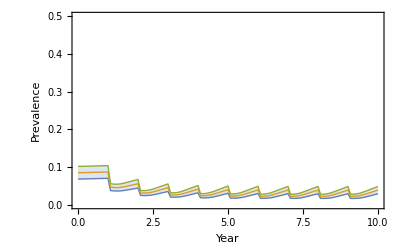
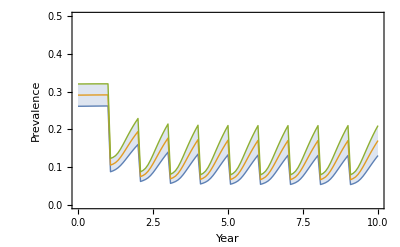
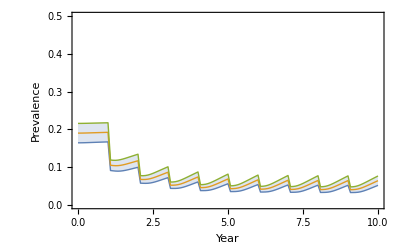
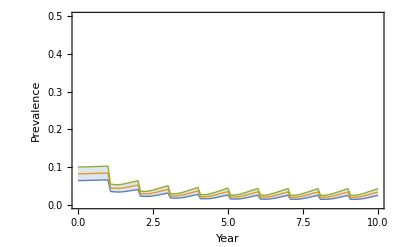
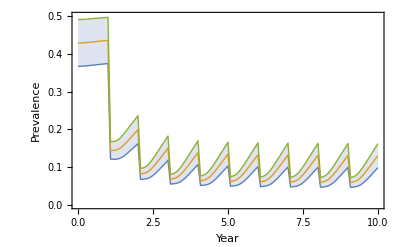
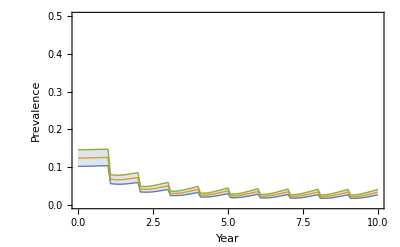
<|CL→-Graphics-,SL→-Graphics-,AL→-Graphics-,CH→-Graphics-,SH→-Graphics-,AH→-Graphics-|>

```mathematica
(*Plot mean +SDD histories*)
PDS[{#[[1]]-#[[2]],#[[1]],#[[1]]+#[[2]]},{0,.5},{Thin,Thick,Thin},{"Year","Prevalence"},Filling->{1->{3}},DataRange->{0,tf}]&/@pLM2
```

## 14 control strategies: base case

### Control strategies

```mathematica
(*CWT*)
CWT[(*coverage*)f_,(*efficacy*)ef_,(*Timing period*)tc_]:=WEr[#,f,ef,tc]&/@{htC,htS,htA};
(*SWT*)
SBT[(*coverage*)f_,(*efficacy*)ef_,(*Timing period*)tc_]:=WEr[htS,f,ef,tc];
(*14 control strategies*)
CT14=
With[{(*Human*)
CWA=CWT[.75,.15,1],
CWB=CWT[.75,.15,.5],
SBA=SBT[.75,.15,1],
SBB=SBT[.75,.15,.5],
(*snail*)
SCA=SCE[stv,.1,1],
SCB=SCE[stv,.1,.5]},
{(*MDA*)CWA,CWB,SBA,SBB,(*snail control*)SCA,SCB,(*integrated control*){CWA,SCA},{CWA,SCB},{CWB,SCA},{CWB,SCB},{SBA,SCA},{SBA,SCB},{SBB,SCA},{SBB,SCB}}];
```

### Ensemble run

```mathematica
(*Generate random environment*)
sebZ=Table[sebR,20];
```

```mathematica
(*CWT with 75% civerage*)
CWA=CWT[.75,.15,1];
```

```mathematica
(*Run history ensemble*)
MST=EnsRun[CWA,.1,0,0];//AbsoluteTiming
```

{15.7058,Null}

### Run Milalani

```mathematica
(*1000 calibrated posterior*)
With[{e1=ESWpar@"Milalani"},
HPost=Thread@Values@e1;
(*par names*)
paN=Symbol/@Keys@e1];
(*parameter dataset*)
With[{(*Random posterior draw*)EHP=RandomSample[HPost,50]},
dkL=Dataset[<|Thread[ToString/@paN->#]|>&/@EHP]];
```

```mathematica
(*Random environment*)
sebZ=Table[sebR,20];
```

```mathematica
(*Run 14*)
RS14=Table[EnsRun[stg,.1,0,0],{stg,CT14}];//AbsoluteTiming
```

{161.909,Null}

```mathematica
Dimensions/@RS14
```

{{122,12},{122,12},{122,12},{122,12},{122,12},{122,12},{122,12},{122,12},{122,12},{122,12},{122,12},{122,12},{122,12},{122,12}}

```mathematica
Export["C:\\Users\\dxg5\\Dropbox\\Schistosomiasis (Case)\\Cost effectiveness\\REVISIONS-PNAS\\New data\\Milalani 14n.xlsx",
"Sheets"->XLS@RS14,"Rules"]
```

C:\Users\dxg5\Dropbox\Schistosomiasis (Case)\Cost effectiveness\REVISIONS-PNAS\New data\Milalani 14n.xlsx

```mathematica
PDS[{#[[1]]-#[[2]],#[[1]],#[[1]]+#[[2]]},{0,.5},{Thin,Thick,Thin},{"Year","Prevalence"},Filling->{1->{3}},DataRange->{0,tf}]&/@MST
```

### Run Mwaembe

```mathematica
(*1000 calibrated posterior*)
With[{e1=ESWpar@"Mwaembe"},
HPost=Thread@Values@e1;
(*par names*)
paN=Symbol/@Keys@e1];
(*parameter dataset*)
With[{(*Random posterior draw*)EHP=RandomSample[HPost,50]},
dkL=Dataset[<|Thread[ToString/@paN->#]|>&/@EHP]];
```

```mathematica
(*Random environment*)
sebZ=Table[sebR,20];
```

```mathematica
(*Run 14*)
RS14=Table[EnsRun[stg,.1,0,0],{stg,CT14}];//AbsoluteTiming
```

{170.462,Null}

```mathematica
Dimensions/@RS14
```

{{122,12},{122,12},{122,12},{122,12},{122,12},{122,12},{122,12},{122,12},{122,12},{122,12},{122,12},{122,12},{122,12},{122,12}}

```mathematica
Export["C:\\Users\\dxg5\\Dropbox\\Schistosomiasis (Case)\\Cost effectiveness\\REVISIONS-PNAS\\New data\\Mwaembe 14n.xlsx",
"Sheets"->XLS@RS14,"Rules"]
```

C:\Users\dxg5\Dropbox\Schistosomiasis (Case)\Cost effectiveness\REVISIONS-PNAS\New data\Mwaembe 14n.xlsx

```mathematica
PDS[{#[[1]]-#[[2]],#[[1]],#[[1]]+#[[2]]},{0,.5},{Thin,Thick,Thin},{"Year","Prevalence"},Filling->{1->{3}},DataRange->{0,tf}]&/@MST
```

## One-way sensitivity

### 10 cases 14 strategies

```mathematica
(*1000 calibrated posterior*)
With[{e1=ESWpar@"Mwaembe"},
HPost=Thread@Values@e1;
(*par names*)
paN=Symbol/@Keys@e1];
(*parameter dataset*)
With[{(*Random posterior draw*)EHP=RandomSample[HPost,50]},
dkL=Dataset[<|Thread[ToString/@paN->#]|>&/@EHP]];
(*Generate Random environment*)
sebZ=Table[sebR,20];
```

#### C1. Snail transport rM/β=.4

```mathematica
(*Run 14*)
RS14=Table[EnsRun[stg,.1,.4,0],{stg,CT14}];//AbsoluteTiming
```

{185.638,Null}

```mathematica
Export["C:\\Users\\dxg5\\Dropbox\\Schistosomiasis (Case)\\Cost effectiveness\\REVISIONS-PNAS\\Mwaembe C1.xlsx",
"Sheets"->XLS@RS14,"Rules"]
```

C:\Users\dxg5\Dropbox\Schistosomiasis (Case)\Cost effectiveness\REVISIONS-PNAS\Mwaembe C1.xlsx

#### C2. External FOI Λe/Λ0 =.4

```mathematica
(*Run 14*)
RS14=Table[EnsRun[stg,.1,0,.4],{stg,CT14}];//AbsoluteTiming
```

{172.869,Null}

```mathematica
Export["C:\\Users\\dxg5\\Dropbox\\Schistosomiasis (Case)\\Cost effectiveness\\REVISIONS-PNAS\\Milalani C2.xlsx",
"Sheets"->XLS@RS14,"Rules"]
```

C:\Users\dxg5\Dropbox\Schistosomiasis (Case)\Cost effectiveness\REVISIONS-PNAS\Milalani C2.xlsx

#### C3. MDA efficacy .25

```mathematica
(*14 control strategies with ef=.25*)
CB14=
With[{(*Human*)
CWA=CWT[.75,.25,1],
CWB=CWT[.75,.25,.5],
SBA=SBT[.75,.25,1],
SBB=SBT[.75,.25,.5],
(*snail*)
SCA=SCE[stv,.1,1],
SCB=SCE[stv,.1,.5]},
{(*MDA*)CWA,CWB,SBA,SBB,(*snail control*)SCA,SCB,(*integrated control*){CWA,SCA},{CWA,SCB},{CWB,SCA},{CWB,SCB},{SBA,SCA},{SBA,SCB},{SBB,SCA},{SBB,SCB}}];
```

```mathematica
(*Run 14*)
RS14=Table[EnsRun[stg,.1,0,0],{stg,CB14}];//AbsoluteTiming
```

{172.439,Null}

```mathematica
Export["C:\\Users\\dxg5\\Dropbox\\Schistosomiasis (Case)\\Cost effectiveness\\REVISIONS-PNAS\\Milalani C3.xlsx",
"Sheets"->XLS@RS14,"Rules"]
```

C:\Users\dxg5\Dropbox\Schistosomiasis (Case)\Cost effectiveness\REVISIONS-PNAS\Milalani C3.xlsx

#### C4. molluscicide efficacy .3

```mathematica
(*14 control strategies with ef=.25*)
CB14=
With[{(*Human*)
CWA=CWT[.75,.15,1],
CWB=CWT[.75,.15,.5],
SBA=SBT[.75,.15,1],
SBB=SBT[.75,.15,.5],
(*snail*)
SCA=SCE[stv,.3,1],
SCB=SCE[stv,.3,.5]},
{(*MDA*)CWA,CWB,SBA,SBB,(*snail control*)SCA,SCB,(*integrated control*){CWA,SCA},{CWA,SCB},{CWB,SCA},{CWB,SCB},{SBA,SCA},{SBA,SCB},{SBB,SCA},{SBB,SCB}}];
```

```mathematica
(*Run 14*)
RS14=Table[EnsRun[stg,.1,0,0],{stg,CB14}];//AbsoluteTiming
```

{172.622,Null}

```mathematica
Export["C:\\Users\\dxg5\\Dropbox\\Schistosomiasis (Case)\\Cost effectiveness\\REVISIONS-PNAS\\Milalani C4.xlsx",
"Sheets"->XLS@RS14,"Rules"]
```

C:\Users\dxg5\Dropbox\Schistosomiasis (Case)\Cost effectiveness\REVISIONS-PNAS\Milalani C4.xlsx

```mathematica
"C:\\Users\\dxg5\\Dropbox\\Schistosomiasis (Case)\\Cost effectiveness\\REVISIONS-PNAS\\Milalani C4.xlsx"
```

C:\Users\dxg5\Dropbox\Schistosomiasis (Case)\Cost effectiveness\REVISIONS-PNAS\Milalani C4.xlsx

#### C5 MDA coverage 85

```mathematica
(*14 control strategies with ef=.25*)
CB14=
With[{(*Human*)
CWA=CWT[.85,.15,1],
CWB=CWT[.85,.15,.5],
SBA=SBT[.85,.15,1],
SBB=SBT[.85,.15,.5],
(*snail*)
SCA=SCE[stv,.1,1],
SCB=SCE[stv,.1,.5]},
{(*MDA*)CWA,CWB,SBA,SBB,(*snail control*)SCA,SCB,(*integrated control*){CWA,SCA},{CWA,SCB},{CWB,SCA},{CWB,SCB},{SBA,SCA},{SBA,SCB},{SBB,SCA},{SBB,SCB}}];
```

```mathematica
(*Run 14*)
RS14=Table[EnsRun[stg,.1,0,0],{stg,CB14}];//AbsoluteTiming
```

{169.338,Null}

```mathematica
Export["C:\\Users\\dxg5\\Dropbox\\Schistosomiasis (Case)\\Cost effectiveness\\REVISIONS-PNAS\\Milalani C5.xlsx",
"Sheets"->XLS@RS14,"Rules"]
```

C:\Users\dxg5\Dropbox\Schistosomiasis (Case)\Cost effectiveness\REVISIONS-PNAS\Milalani C5.xlsx

```mathematica
"C:\\Users\\dxg5\\Dropbox\\Schistosomiasis (Case)\\Cost effectiveness\\REVISIONS-PNAS\\Milalani C5.xlsx"
```

C:\Users\dxg5\Dropbox\Schistosomiasis (Case)\Cost effectiveness\REVISIONS-PNAS\Milalani C5.xlsx

#### C6 MDA coverage 50-75-50

```mathematica
(*Mixed CWT*)
CWZ[(*coverage*){fC_,fS_,fA_},(*efficacy*)ef_,(*Timing period*)tc_]:=
{WEr[htC,fC,ef,tc],WEr[htS,fS,ef,tc],WEr[htA,fA,ef,tc]}
```

```mathematica
(*14 control strategies with ef=.25*)
CB14=
With[{(*Human*)
CWA=CWZ[{.5,.75,.5},.15,1],
CWB=CWZ[{.5,.75,.5},.15,.5],
SBA=SBT[.75,.15,1],
SBB=SBT[.75,.15,.5],
(*snail*)
SCA=SCE[stv,.1,1],
SCB=SCE[stv,.1,.5]},
{(*MDA*)CWA,CWB,SBA,SBB,(*snail control*)SCA,SCB,(*integrated control*){CWA,SCA},{CWA,SCB},{CWB,SCA},{CWB,SCB},{SBA,SCA},{SBA,SCB},{SBB,SCA},{SBB,SCB}}];
```

```mathematica
(*Run 14*)
RS14=Table[EnsRun[stg,.1,0,0],{stg,CB14}];//AbsoluteTiming
```

{173.535,Null}

```mathematica
Export["C:\\Users\\dxg5\\Dropbox\\Schistosomiasis (Case)\\Cost effectiveness\\REVISIONS-PNAS\\Milalani C6.xlsx",
"Sheets"->XLS@RS14,"Rules"]
```

C:\Users\dxg5\Dropbox\Schistosomiasis (Case)\Cost effectiveness\REVISIONS-PNAS\Milalani C6.xlsx

```mathematica
"C:\\Users\\dxg5\\Dropbox\\Schistosomiasis (Case)\\Cost effectiveness\\REVISIONS-PNAS\\Milalani C6.xlsx"
```

C:\Users\dxg5\Dropbox\Schistosomiasis (Case)\Cost effectiveness\REVISIONS-PNAS\Milalani C6.xlsx

#### C7. Full compliance

```mathematica
(*Run 14*)
RS14=Table[EnsRun[stg,0,0,0],{stg,CT14}];//AbsoluteTiming
```

{164.124,Null}

```mathematica
Export["C:\\Users\\dxg5\\Dropbox\\Schistosomiasis (Case)\\Cost effectiveness\\REVISIONS-PNAS\\Milalani C7.xlsx",
"Sheets"->XLS@RS14,"Rules"]
```

C:\Users\dxg5\Dropbox\Schistosomiasis (Case)\Cost effectiveness\REVISIONS-PNAS\Milalani C7.xlsx

```mathematica
"C:\\Users\\dxg5\\Dropbox\\Schistosomiasis (Case)\\Cost effectiveness\\REVISIONS-PNAS\\Milalani C7.xlsx"
```

C:\Users\dxg5\Dropbox\Schistosomiasis (Case)\Cost effectiveness\REVISIONS-PNAS\Milalani C7.xlsx

#### C8 MDA coverage 50

```mathematica
(*14 control strategies with ef=.25*)
CB14=
With[{(*Human*)
CWA=CWT[.5,.15,1],
CWB=CWT[.5,.15,.5],
SBA=SBT[.5,.15,1],
SBB=SBT[.5,.15,.5],
(*snail*)
SCA=SCE[stv,.1,1],
SCB=SCE[stv,.1,.5]},
{(*MDA*)CWA,CWB,SBA,SBB,(*snail control*)SCA,SCB,(*integrated control*){CWA,SCA},{CWA,SCB},{CWB,SCA},{CWB,SCB},{SBA,SCA},{SBA,SCB},{SBB,SCA},{SBB,SCB}}];
```

```mathematica
(*Run 14*)
RS14=Table[EnsRun[stg,.1,0,0],{stg,CB14}];//AbsoluteTiming
```

{167.839,Null}

```mathematica
Export["C:\\Users\\dxg5\\Dropbox\\Schistosomiasis (Case)\\Cost effectiveness\\REVISIONS-PNAS\\Milalani C8.xlsx",
"Sheets"->XLS@RS14,"Rules"]
```

C:\Users\dxg5\Dropbox\Schistosomiasis (Case)\Cost effectiveness\REVISIONS-PNAS\Milalani C8.xlsx

#### C9 Low (N,b)

```mathematica
(*Equil snail input: n=total controlled by ν/β, c=patency fraction*)
EqS[{n_,y_,c_}]={n-(1+c)y,y,c y};
(*Random snail inputs {y,c} with fixed N *)
RaS[n_]:=Prepend[RandomReal[#]&/@{{.15,.45},{.05,.15}},n]
(*Random env/behav: ωC, ωA with fixed b*)
ReB[b_]:=Prepend[RandomReal[#]&/@{{.2,1},{.2,1.2}},b]
(*snail-env input*)
SebR[n_,b_]:=Join[EqS@RaS@n,ReB@b];
```

```mathematica
(*14 control strategies*)
CT14=
With[{(*Human*)
CWA=CWT[.75,.15,1],
CWB=CWT[.75,.15,.5],
SBA=SBT[.75,.15,1],
SBB=SBT[.75,.15,.5],
(*snail*)
SCA=SCE[stv,.1,1],
SCB=SCE[stv,.1,.5]},
{(*MDA*)CWA,CWB,SBA,SBB,(*snail control*)SCA,SCB,(*integrated control*){CWA,SCA},{CWA,SCB},{CWB,SCA},{CWB,SCB},{SBA,SCA},{SBA,SCB},{SBB,SCA},{SBB,SCB}}];
```

```mathematica
(*Generate Random environment*)
sebZ=Table[SebR[.6,.5],20];
```

```mathematica
(*Run 14*)
RS14=Table[EnsRun[stg,.1,0,0],{stg,CB14}];//AbsoluteTiming
```

{166.914,Null}

```mathematica
Export["C:\\Users\\dxg5\\Dropbox\\Schistosomiasis (Case)\\Cost effectiveness\\REVISIONS-PNAS\\Mwaembe C9.xlsx",
"Sheets"->XLS@RS14,"Rules"]
```

C:\Users\dxg5\Dropbox\Schistosomiasis (Case)\Cost effectiveness\REVISIONS-PNAS\Mwaembe C9.xlsx

#### C10 high (N,b)

```mathematica
(*Generate Random environment*)
sebZ=Table[SebR[.95,3],20];
```

```mathematica
(*Run 14*)
RS14=Table[EnsRun[stg,.1,0,0],{stg,CB14}];//AbsoluteTiming
```

{182.655,Null}

```mathematica
Export["C:\\Users\\dxg5\\Dropbox\\Schistosomiasis (Case)\\Cost effectiveness\\REVISIONS-PNAS\\Mwaembe C10.xlsx",
"Sheets"->XLS@RS14,"Rules"]
```

C:\Users\dxg5\Dropbox\Schistosomiasis (Case)\Cost effectiveness\REVISIONS-PNAS\Mwaembe C10.xlsx